## Formulae an

```mathematica
MpgChain[g_]:=Block[{contract, result},
If[VertexCount[g]==3,Return[{ChromaticPolynomial[g,4]/24}]];
Table[
contract=EdgeContract[g,e];
If[MaximalPlanarQ[contract],
result=Prepend[MpgChain[contract],{e,ChromaticPolynomial[g,4]/24}];
Goto[stop]
]
,{e,EdgeList[g]}
];
Label[stop];
result
]
```

```mathematica
MpgChain3[g_]:=Block[{contract, result},
If[VertexCount[g]==3,Return[{ChromaticPolynomial[g,4]/24}]];
Table[
contract=EdgeContract[g,e];
If[MaximalPlanarQ[contract],
result=Prepend[MpgChain3[contract],ChromaticPolynomial[g,4]/24];
Goto[stop]
]
,{e,EdgeList[g]}
];
Label[stop];
result
]
```

```mathematica
Monitor[Select[Table[k->With[{l=Differences[Reverse[MpgChain3[ReadGrof[k]]]]},{Min[l],Max[l]}],{k,10}],#[[2]]≠{0,0}&],k]
```

{4→{0,3},6→{0,3},7→{0,3}}

```mathematica
Clear[MpgChain2]
```

```mathematica
MpgChain2[g_,previous_:{}, positions_:Null]:=Block[{contract, result, coord, newPos=positions, layout},
If[VertexCount[g]==3,Return[{Labeled[Graph[g,ImageSize->300,GraphLayout->"PlanarEmbedding",VertexLabelStyle->Directive[Darker[Green],Italic,20],VertexLabels->"Name",GraphHighlightStyle->"Thick",GraphHighlight->CollectMPGEdges[g]],{ChromaticPolynomial[g,4]/24,Map[VertexDegree[g,#]&,VertexList[g]]}]}]];
Table[
contract=EdgeContract[g,e];
If[MaximalPlanarQ[contract],
If[positions==Null,
layout = Graph[
g,
GraphLayout->"TutteEmbedding",
GraphHighlightStyle->"Thick",
VertexLabels->"Name",
GraphHighlight->Select[CollectMPGEdges[g],#=!=e&],
VertexLabelStyle->Directive[Darker[Green],Italic,20],
ImageSize->300, 
EdgeStyle->{e->{Thick,Blue,Dashed}}, 
VertexStyle->Map[#->Yellow&,previous], 
VertexSize->Map[#->Large&,previous]
];
newPos=Options[g, VertexCoordinates];
Print[newPos];
Interrupt[];
];
result=Prepend[MpgChain2[contract,{e[[1]]}, positions],{e,Labeled[
Graph[
g,
GraphLayout->"TutteEmbedding",
GraphHighlightStyle->"Thick",
VertexLabels->"Name",
GraphHighlight->Select[CollectMPGEdges[g],#=!=e&],
VertexLabelStyle->Directive[Darker[Green],Italic,20],
ImageSize->300, 
EdgeStyle->{e->{Thick,Blue,Dashed}}, 
VertexStyle->Map[#->Yellow&,previous], 
VertexSize->Map[#->Large&,previous],
VertexCoordinates->If[positions==Null,Automatic,]
],{Column[ExplainContractionCounts[g,e]],Style[ChromaticPolynomial[g,4]/24,Green ],Map[VertexDegree[g,#]&,VertexList[g]]}]}];
Goto[stop]
]
,{e,EdgeList[g]}
];
Label[stop];
result
]
```

## experiments come

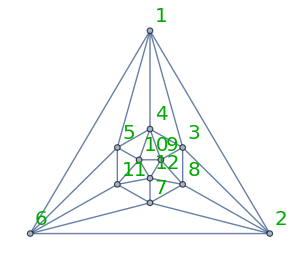
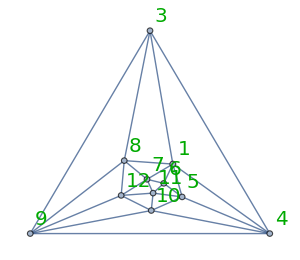
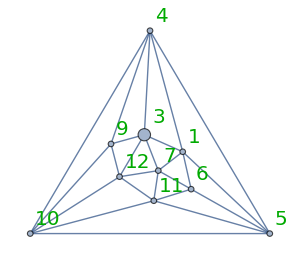
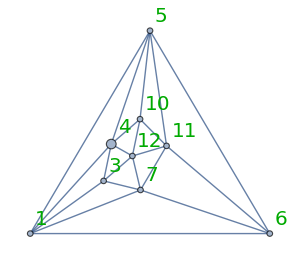
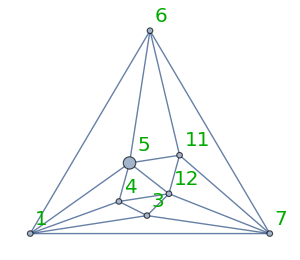
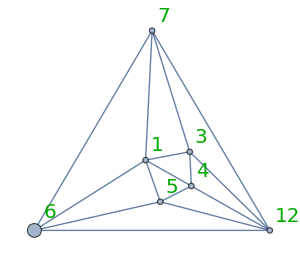
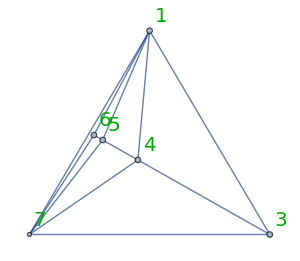
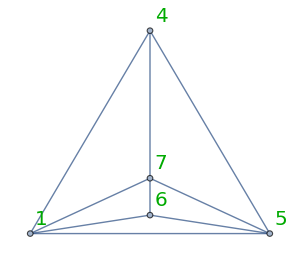
{{1<->2,-Graphics-{4
24,10,{5,5,5,5,5,5,5,5,5,5,5,5}}},{3<->8,-Graphics-{4
17,8,{4,5,5,4,5,5,5,5,5,5,6}}},{4<->9,-Graphics-{3
12,8,{5,5,4,5,4,5,5,5,5,5}}},{5<->10,-Graphics-{2
8,2,{5,4,5,4,5,5,5,4,5}}},{6<->11,-Graphics-{2
4,3,{4,5,4,5,5,4,4,5}}},{7<->12,-Graphics-{0
3,5,{4,5,5,4,4,4,4}}},{3<->1,-Graphics-{0
1,1,{5,3,4,4,3,5}}},{5<->4,-Graphics-{0
0,1,{3,4,3,4,4}}},{7<->6,-Graphics-{0
0,1,{3,3,3,3}}},-Graphics-{1,{2,2,2}}}

```mathematica
MpgChain2[Graph[plantri [[1]] ] ]
```

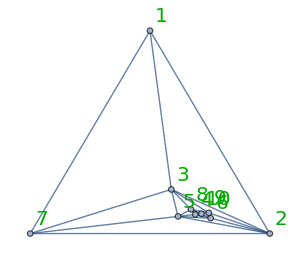
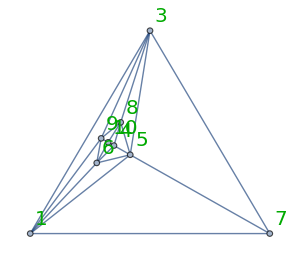
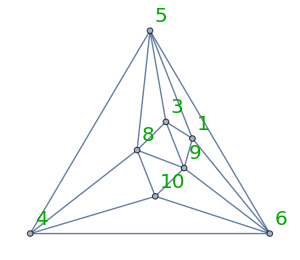
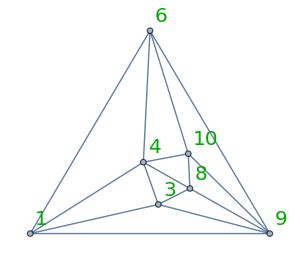
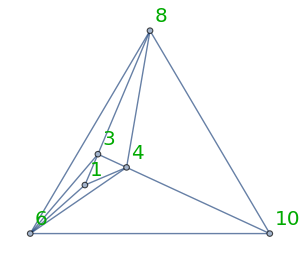
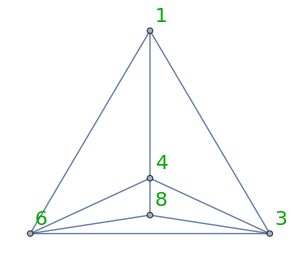
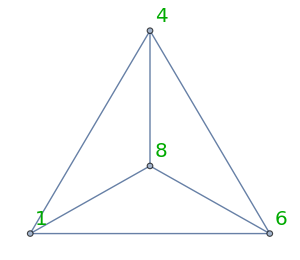
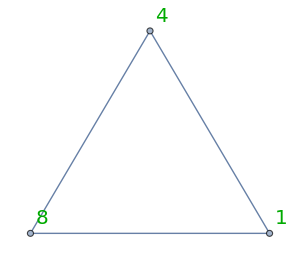
{{1<->2,-Graphics-{3
12,3,{3,6,6,4,6,5,5,5,4,4}}},{3<->7,-Graphics-{3
7,3,{5,3,6,5,5,5,4,4,5}}},{4<->5,-Graphics-{1
5,3,{5,5,5,5,4,4,4,4}}},{6<->9,-Graphics-{0
3,5,{4,5,4,4,4,4,5}}},{8<->10,-Graphics-{1
0,1,{4,3,3,4,5,5}}},{3<->1,-Graphics-{0
0,1,{3,4,4,4,3}}},{6<->4,-Graphics-{0
0,1,{3,3,3,3}}},-Graphics-{1,{2,2,2}}}

```mathematica
MpgChain2[ReadGrof[99] ]
```